```mathematica
l=4;
tryit=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}]
FullSimplify[Abs[Sin[h]]*LegendreQ[l,1,Cos[h]],{h>0}];
god=D[tryit,h]/Sin[h];
Series[god,{h,0,1}];
(*Plot[tryit,{h,0,Pi}]
Plot[god,{h,0,Pi}]*)
```

-5/4 Cos[h] (1+7 Cos[2 h]) Sin[h]^2

InterpolatingFunction[{{0.00552428,1.563}},<>]

InterpolatingFunction[{{0.00552428,1.563}},<>]

InterpolatingFunction[{{0.00552428,1.563}},<>]

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

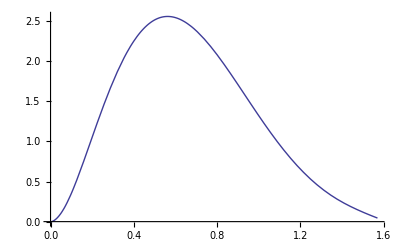

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

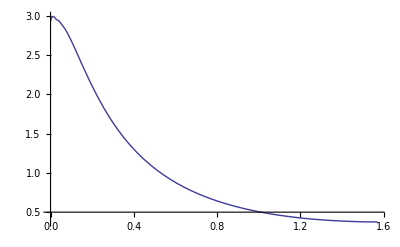

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

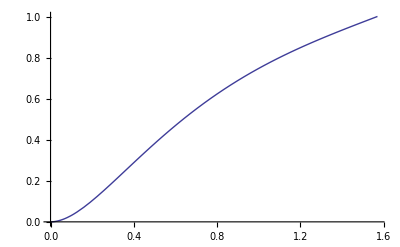

```mathematica
lst=ReadList[NotebookDirectory[]<>"aphi0.9999.txt",Number,RecordLists->True];
lsttran=Transpose[lst];
hlist=lsttran[[1]];
aphilist=lsttran[[2]];
residlist=lsttran[[3]];
brlist=lsttran[[4]];
haphilist=Partition[Riffle[hlist,aphilist],2];
hresidlist=Partition[Riffle[hlist,residlist],2];
hbrlist=Partition[Riffle[hlist,brlist],2];
aphinum=Interpolation[haphilist]
residnum=Interpolation[hresidlist]
brnum=Interpolation[hbrlist]
Plot[residnum[h],{h,0,Pi/2}]
Plot[brnum[h],{h,0,Pi/2}]
Plot[aphinum[h],{h,0,Pi/2}]
```

```mathematica
aphinum[h]/.h->1
```

0.748942

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(1.02848+0.9998 Cos[h]^2)Csc[h] (Sin[h]+1.10363 Cos[h]^2 Sin[h]+2.835 Cos[h] (0.06 Cos[h]+0.45 Cos[h]^3.5+0. Cos[h]^5+0.94 Cos[h]^14) Sin[h]-0.551815 Sin[h]^3+1.4175 Sin[h]^2 (-0.06 Sin[h]-1.575 Cos[h]^2.5 Sin[h]+0. Cos[h]^4 Sin[h]-13.16 Cos[h]^13 Sin[h]))

InterpolatingFunction::dmval: Input value {0.00003208912496166717`} lies outside the range of data in the interpolating function. Extrapolation will be used.

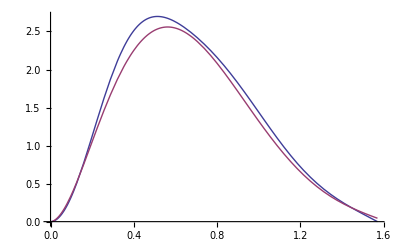

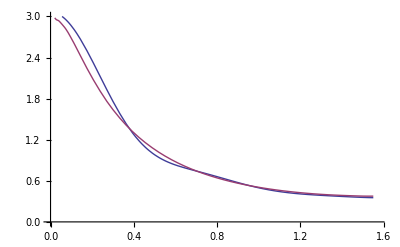

```mathematica
(* QUADRUPOLAR EXPANSION *)
(* Weight of quadrupolar Jon's term *)
ac=0.1;
a=0.9999;
aphi4Jon:=6.5(ac*5/4 Cos[h] (1+7 Cos[2 h]) Sin[h]^2+(1-ac)Sin[h]^2*Cos[h]);
(* SASHA'S BY-EYE FIT *)
pow1=14;
pow2=5;
pow4=3.5;
coef2=0.0;
coef3=0.06;
coef4=0.45;
coef1=1.45-coef2-coef3-coef4;
aphi4:=(24*Sin[h]^2*(coef1*Cos[h]^pow1+coef2*Cos[h]^pow2+coef4*Cos[h]^pow4+coef3*Cos[h]^1))
(*
l=2;Aphi4a=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}];
l=4;Aphi4b=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}];
l=6;Aphi4c=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}];
l=8;Aphi4d=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}];
aphi4:=1*(D1*Aphi4a+D2*Aphi4b+D3*Aphi4c+D4*Aphi4d)*)
(* COMPUTE B^r *)
rh=1+Sqrt[1-a^2];
omh=a/(2rh);
sigma=rh^2+a^2 Cos[h]^2;
aphi0=1-Cos[h];
aphi2=(2*(-49+6*Pi^2))/9.*Sin[h]^2*Cos[h];
aphi=aphi0+omh^2*aphi2+omh^4*aphi4;
aphiJon=aphi0+omh^2*aphi2+omh^4*aphi4Jon;
gdet=sigma Sin[h];
Brtemp[h_]=D[aphi,h]/gdet;
(*sol=Solve[{Brtemp[0.00001]==3,Brtemp[0.5]==brnum[0.5],Brtemp[0.7]==brnum[0.7],Brtemp[Pi/2]==brnum[Pi/2]},{D1,D2,D3,D4}]*)
(*sol=Solve[{Brtemp[0.00001]==3,Brtemp[0.5]==brnum[0.5],Brtemp[1.0]==brnum[1.0],Brtemp[Pi/2]==brnum[Pi/2]},{D1,D2,D3,D4}]*)
(*sol={D1->2.72329,D2->1.33978,D3->0.371329,D4->0.120496}*)
Br=(Brtemp[h]/.sol)[[1]]
Brnum:=aphinum'[h]/gdet;
BrJon=D[aphiJon,h]/gdet;
Plot[{aphi4,residnum[h]},{h,0,Pi/2}]
Plot[{Br,brnum[h]},{h,0.02,Pi/2-0.02},PlotRange->{{0,Pi/2},{0,3}}]
```

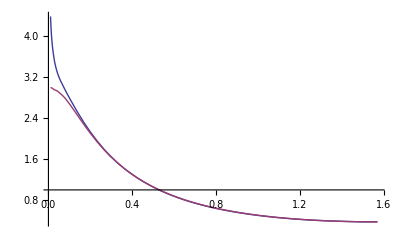

```mathematica
Plot[{Brnum,brnum[h]},{h,0.01,Pi/2}]
```

```mathematica
Brtemp[1.]/.sol
sol=Solve[{Brtemp[0.0001]==3,Brtemp[0.5]==brnum[0.5],Brtemp[1]==brnum[1],Brtemp[Pi/2]==brnum[Pi/2]},{D1,D2,D3,D4}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.497923/.sol

InterpolatingFunction::dmval: Input value {π/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

{}

```mathematica
(Brtemp[h]/.sol)[[1]]
```

1/(1.02848+0.9998 Cos[h]^2)